```mathematica
Needs["Combinatorica`"];
```

```mathematica
ValidPartitionQ[partition_]:=VectorQ[partition,(IntegerQ[#]&&NonNegative[#])&]&&Apply[GreaterEqual,partition]
```

```mathematica
EncodeDiagram[partition_List?ValidPartitionQ]:=
Module[{par= partition},
Flatten[Prepend[Append[
Map[Append[ConstantArray[0,#],1]&,
	Abs[Differences[par]]],{0,1}],{0,1}]]
]

SequenceCenter [seq_List]:=Module[ {n=1},
While[Count[seq[[;;n]],1]!=Count[seq[[n+1;;]],0],n++];
Return[{n,n+1}]]



AbacusDiagram[seq_List,div_Integer]:=Module[
{s=seq, p=div,  center =  SequenceCenter[seq] , lhs,rhs, above, below},
lhs =s[[;;center[[1]]]] ;
rhs = s[[center[[2]];;]] ;
above = Partition[PadLeft[lhs,(Quotient[Length[lhs],p]+2)*p,0],p];
below = Partition[PadRight[rhs,(Quotient[Length[rhs],p]+2)*p,1],p];
Return[Join[above,below]]
]

BeadSlide[abacus_List]:=Module[{trans =Transpose[abacus]},
Transpose[Map[PadLeft[ConstantArray[1,Count[#,1]],Length[#]]&,trans ]]
]


pCoreTrivialityQ[seq_List]:=Module[{s=seq},

If[Total[Abs[Differences[Flatten[s]]]]==1,1,0]
]
```

```mathematica
EncodeDiagram[{5,5,4,1,1}]
```

{0,1,1,0,1,0,0,0,1,1,0,1}

```mathematica
seq={0,1,1,0,1,0,0,0,1,1,0,1}
```

{0,1,1,0,1,0,0,0,1,1,0,1}

```mathematica
SequenceCenter[{0,1,1,0,1,0,0,0,1,1,0,1}]
```

{6,7}

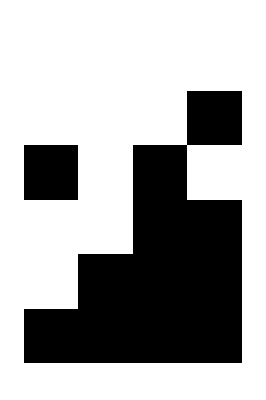

```mathematica
AbacusDiagram[seq,p]//ArrayPlot
```

```mathematica
BeadSlide[AbacusDiagram[seq,p]]
```

{0,0,0,0,0,0,0,0,0,1,0,-1,0,1,0,0,0,0,0,0,0,0,0}

```mathematica
pCoreTrivialityQ[BeadSlide[AbacusDiagram[seq,p]]]
```

0